# LF holographic QCD

## Analytical structures of GPDs of the nucleon and pion

## Initialization

```mathematica
Clear["Global`*"];
```

```mathematica
Format[x,TraditionalForm]:=Style["x",FontColor->Blue];
Format[kt,TraditionalForm]:=Style["k_⊥",FontColor->Blue];
Format[Q,TraditionalForm]:=Style["Q",FontColor->Blue];
Format[Q2,TraditionalForm]:=Style["Q^2",FontColor->Blue];
Format[t,TraditionalForm]:=Style["t",FontColor->Blue];
Format[qt,TraditionalForm]:=Style["q_⊥",FontColor->Blue];
Format[bt,TraditionalForm]:=Style["b_⊥",FontColor->Cyan];
Format[ζ,TraditionalForm]:=Style["ζ",FontColor->Cyan];
Format[z,TraditionalForm]:=Style["z",FontColor->Cyan];
Format[mq,TraditionalForm]:=Style["m_q",FontColor->Orange];
Format[mD,TraditionalForm]:=Style["mD",FontColor->Orange];
Format[η,TraditionalForm]:=Style["η",FontColor->Orange];
Format[λ,TraditionalForm]:=Style["λ",FontColor->Orange];
Format[κ,TraditionalForm]:=Style["κ",FontColor->Orange];
Format[τ,TraditionalForm]:=Style["τ",FontColor->Magenta];
```

```mathematica
Γ=Gamma;
Β=Beta;(*Beta*)
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
dir="/Users/user/Liu/Repos/LFHQCD/notebook/";
```

## General

### Massless

Form factor

```mathematica
FF[Q2_,τ_,λ_]:=Γ[τ-1/2]/(√π Γ[τ-1]) Β[τ-1,Q2/(4 λ)+1/2];
```

GPD

```mathematica
w[x_]:=x^(1-x) Exp[-a (1-x)^2];
GPD[x_,Q2_,τ_,λ_]:=Γ[τ-1/2]/(√π Γ[τ-1]) w[x]^(Q2/(4 λ)-1/2)(1-w[x])^(τ-2) w'[x];
IPD[x_,b2_,τ_,λ_]:=Γ[τ-1/2]/(√π Γ[τ-1])λ/(π Log[1/w[x]])Exp[-b2 λ/Log[1/w[x]]] w[x]^(-1/2)(1-w[x])^(τ-2) w'[x];
```

```mathematica
Plot[w[x]/.{a->a0},{}]
```

## Pion

```mathematica
λ0=0.5482^2;
a0=0.507;
a1=0.541;
a2=0.473;
```

```mathematica
F["pion"][Q2_]:=(((1-γ) FF[Q2,2,λ0]+γ FF[Q2,4,λ0])/.{γ->0.125});
H["pion"]["v"][x_,Q2_]:=(((1-γ) GPD[x,Q2,2,λ0]+γ GPD[x,Q2,4,λ0])/.{γ->0.125,a->a0});
Η["pion"]["v"][x_,b2_]:=(((1-γ) IPD[x,b2,2,λ0]+γ IPD[x,b2,4,λ0])/.{γ->0.125,a->a0});
```

```mathematica
Η["pion"]["v"][0.5,]
```

-0.0384776

```mathematica
H["pion"]["v"][x,b]
```

0.4375 (ⅇ^(-0.507 (1-x)^2) x^(1-x))^(-1/2+0.831882 b) (1.014 ⅇ^(-0.507 (1-x)^2) (1-x) x^(1-x)+ⅇ^(-0.507 (1-x)^2) x^(1-x) ((1-x)/x-Log[x]))+0.117188 (ⅇ^(-0.507 (1-x)^2) x^(1-x))^(-1/2+0.831882 b) (1-ⅇ^(-0.507 (1-x)^2) x^(1-x))^2 (1.014 ⅇ^(-0.507 (1-x)^2) (1-x) x^(1-x)+ⅇ^(-0.507 (1-x)^2) x^(1-x) ((1-x)/x-Log[x]))

```mathematica
Clear[grid];
grid={};
For[i=0,i<100,i=i+1,
XX=0+0.2 i;
YY=XX F["pion"][XX];
grid=Join[grid,{{XX,YY}}]];
Export[dir<>"grid_pion_ff.dat",grid,"Table"];
Clear[grid,XX,YY,i];
```

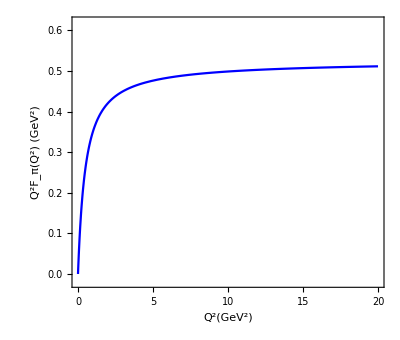

```mathematica
fig["pion FF"]=Plot[Q2 F["pion"][Q2],{Q2,0,20},PlotRange->{-0.02,0.62},Frame->True,FrameStyle->Thickness[0.003],LabelStyle->16,AspectRatio->0.85,PlotStyle->{Blue,Thickness[0.004]},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^2F_π(Q^2) (GeV^2)",18]}]
```

```mathematica
Clear[grid];
grid={};
For[i=0,i<100,i=i+1,
XX=0.005+0.01 i;
a0=0.507;
YY={XX H["pion"]["v"][XX,1],XX H["pion"]["v"][XX,4],XX H["pion"]["v"][XX,10]};
a0=0.541;
YY1={XX H["pion"]["v"][XX,1],XX H["pion"]["v"][XX,4],XX H["pion"]["v"][XX,10]};
a0=0.473;
YY2={XX H["pion"]["v"][XX,1],XX H["pion"]["v"][XX,4],XX H["pion"]["v"][XX,10]};
grid=Join[grid,{{XX,YY[[1]],YY1[[1]],YY2[[1]],YY[[2]],YY1[[2]],YY2[[2]],YY[[3]],YY1[[3]],YY2[[3]]}}]];
Export[dir<>"grid_pion_gpd.dat",grid,"Table"];
Clear[grid,XX,YY,YY1,YY2,i];
```

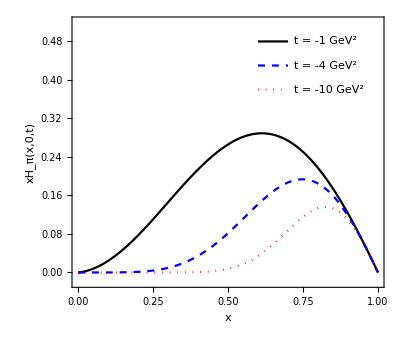

```mathematica
a0=0.507;
fig["pion GPD"]=Show[Plot[{x H["pion"]["v"][x,1],x H["pion"]["v"][x,4], x H["pion"]["v"][x,10]},{x,0,1},Frame->True,FrameStyle->Thickness[0.003],PlotStyle->{{Black,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Dotted,Thickness[0.004]}},LabelStyle->16,AspectRatio->0.85,PlotRange->{Full,{-0.02,0.52}},FrameLabel->{Style["x",18],Style["xH_π(x,0,t)",18]},Axes->True,LabelStyle->12],
Graphics[{{Black,Thickness[0.004],Line[{{0.6,0.48},{0.7,0.48}}]},{FontSize->14,Text["t = -1 GeV^2",{0.72,0.48},Left]}}],
Graphics[{{Blue,Thickness[0.004],Dashed,Line[{{0.6,0.43},{0.7,0.43}}]},{FontSize->14,Text["t = -4 GeV^2",{0.72,0.43},Left]}}],
Graphics[{{Red,Thickness[0.004],Dotted,Line[{{0.6,0.38},{0.7,0.38}}]},{FontSize->14,Text["t = -10 GeV^2",{0.72,0.38},Left]}}]]
```

```mathematica
Clear[grid];
grid={};
a0=0.507;
For[i=0,i<100,i=i+1,
XX=0.005+0.01 i;
For[j=0,j<100,j=j+1,
YY=0.05+0.1 j;
ZZ=H["pion"]["v"][XX,YY]/H["pion"]["v"][XX,0];
grid=Join[grid,{{XX,YY,ZZ}}]]]
Export[dir<>"grid3d_pion_gpd.dat",grid,"Table"];
Clear[grid,XX,YY,i,j];
```

```mathematica
a0=0.507;
CoolColor[z_]:=RGBColor[z,1-z,1];
fig["pion GPD/PDF"]=Plot3D[H["pion"]["v"][x,Q2]/H["pion"]["v"][x,0],{x,0,1},{Q2,10,0},LabelStyle->{16},BoxRatios->{1,1,0.5},PlotRange->{Full,Full,{-0.02,1.02}},Axes->True,LabelStyle->12,AxesLabel->{Style["x",18],Style["-t (GeV^2)",18]},PlotLabel->Style["H_π(x,0,t)/H_π(x,0,0)",18],ColorFunction->CoolColor,BaseStyle->{FontFamily->"Arial"}]
```

-Graphics3D-

```mathematica
a0=0.507;
CoolColor[z_]:=RGBColor[z,1-z,1];
fig["pion IPD"]=Plot3D[Η["pion"]["v"][x,b2]/.{b2->b^2},{x,0,1},{b,-1,1},LabelStyle->{16},BoxRatios->{1,1,0.5},PlotRange->{Full,Full,{0,0.5}},Axes->True,LabelStyle->12,AxesLabel->{Style["x",18],Style["b (GeV^-1)",18]},PlotLabel->Style["H(x,0,b) (GeV^2)",18],ColorFunction->CoolColor,BaseStyle->{FontFamily->"Arial"},PlotPoints->{100,20}]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/notebook/pion_ff.png",fig["pion FF"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/pion_gpd.png",fig["pion GPD"]];
```

## Nucleon

```mathematica
λ0=0.5482^2;
a0=0.507;
a1=0.541;
a2=0.473;
```

```mathematica
F["proton"]["1"][Q2_]:=FF[Q2,3,λ0];
F["neutron"]["1"][Q2_]:=((-r/3 (FF[Q2,3,λ0]-FF[Q2,4,λ0]))/.{r->1.5});
F["proton"]["2"][Q2_]:=((Xp ((1-γp) FF[Q2,4,λ0]+γp FF[Q2,6,λ0]))/.{Xp->1.793,γp->0.27});
F["neutron"]["2"][Q2_]:=((Xn ((1-γn) FF[Q2,4,λ0]+γn FF[Q2,6,λ0]))/.{Xn->-1.913,γn->0.38});
```

```mathematica
H["proton"]["u"][x_,Q2_]:=(((2-r/3) GPD[x,Q2,3,λ0]+r/3 GPD[x,Q2,4,λ0])/.{r->1.5,a->a0});
H["proton"]["d"][x_,Q2_]:=(((1-(2 r)/3) GPD[x,Q2,3,λ0]+(2 r)/3 GPD[x,Q2,4,λ0])/.{r->1.5,a->a0});
Η["proton"]["u"][x_,b2_]:=(((2-r/3) IPD[x,b2,3,λ0]+r/3 IPD[x,b2,4,λ0])/.{r->1.5,a->a0});
Η["proton"]["d"][x_,b2_]:=(((1-(2 r)/3) IPD[x,b2,3,λ0]+(2 r)/3 IPD[x,b2,4,λ0])/.{r->1.5,a->a0});
EE["proton"]["u"][x_,Q2_]:=(((2 Xp (1-γp)+Xn (1-γn)) GPD[x,Q2,4,λ0]+(2 Xp γp+Xn γn) GPD[x,Q2,6,λ0])/.{Xp->1.793,Xn->-1.913,γp->0.27,γn->0.38,a->a0});
EE["proton"]["d"][x_,Q2_]:=(((2 Xn (1-γn)+Xp (1-γp)) GPD[x,Q2,4,λ0]+(2 Xn γn+Xp γp) GPD[x,Q2,6,λ0])/.{Xp->1.793,Xn->-1.913,γp->0.27,γn->0.38,a->a0});
```

```mathematica
a0=0.507;
Print["A(0)^u=",NIntegrate[x (H["proton"]["u"][x,0]),{x,0,1}],"\n",
"A(0)^d=",NIntegrate[x (H["proton"]["d"][x,0]),{x,0,1}]]
a0=0.541;
Print["A(0)^u=",NIntegrate[x (H["proton"]["u"][x,0]),{x,0,1}],"\n",
"A(0)^d=",NIntegrate[x (H["proton"]["d"][x,0]),{x,0,1}]]
a0=0.473;
Print["A(0)^u=",NIntegrate[x (H["proton"]["u"][x,0]),{x,0,1}],"\n",
"A(0)^d=",NIntegrate[x (H["proton"]["d"][x,0]),{x,0,1}]]
```

A(0)^u=0.342344
A(0)^d=0.13708

A(0)^u=0.346976
A(0)^d=0.139191

A(0)^u=0.337704
A(0)^d=0.134972

```mathematica
a0=0.507;
Print["B(0)^u=",NIntegrate[x (EE["proton"]["u"][x,0]),{x,0,1}],"\n",
"B(0)^d=",NIntegrate[x (EE["proton"]["d"][x,0]),{x,0,1}]]
a0=0.541;
Print["B(0)^u=",NIntegrate[x (EE["proton"]["u"][x,0]),{x,0,1}],"\n",
"B(0)^d=",NIntegrate[x (EE["proton"]["d"][x,0]),{x,0,1}]]
a0=0.473;
Print["B(0)^u=",NIntegrate[x (EE["proton"]["u"][x,0]),{x,0,1}],"\n",
"B(0)^d=",NIntegrate[x (EE["proton"]["d"][x,0]),{x,0,1}]]
```

B(0)^u=0.218983
B(0)^d=-0.237076

B(0)^u=0.222421
B(0)^d=-0.240992

B(0)^u=0.215551
B(0)^d=-0.233172

```mathematica
a0=0.507;
Print["2 J^u=",NIntegrate[x (H["proton"]["u"][x,0]+EE["proton"]["u"][x,0]),{x,0,1}],"\n",
"2 J^d=",NIntegrate[x (H["proton"]["d"][x,0]+EE["proton"]["d"][x,0]),{x,0,1}]];
a0=0.541;
Print["2 J^u=",NIntegrate[x (H["proton"]["u"][x,0]+EE["proton"]["u"][x,0]),{x,0,1}],"\n",
"2 J^d=",NIntegrate[x (H["proton"]["d"][x,0]+EE["proton"]["d"][x,0]),{x,0,1}]];
a0=0.473;
Print["2 J^u=",NIntegrate[x (H["proton"]["u"][x,0]+EE["proton"]["u"][x,0]),{x,0,1}],"\n",
"2 J^d=",NIntegrate[x (H["proton"]["d"][x,0]+EE["proton"]["d"][x,0]),{x,0,1}]]
```

2 J^u=0.561327
2 J^d=-0.0999962

2 J^u=0.569396
2 J^d=-0.101801

2 J^u=0.553255
2 J^d=-0.0982008

```mathematica
Print["d/u(x)=",Limit[H["proton"]["d"][x,0]/H["proton"]["u"][x,0],x->1]]
```

d/u(x)=0.

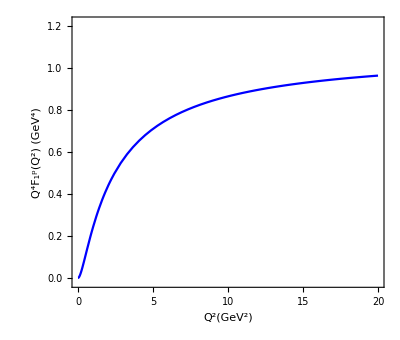

```mathematica
fig["proton FF"]["1"]=Plot[Q2^2 F["proton"]["1"][Q2],{Q2,0,20},PlotRange->{-0.02,1.22},Frame->True,FrameStyle->Thickness[0.003],LabelStyle->16,AspectRatio->0.85,PlotStyle->{Blue,Thickness[0.004]},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^4F_1^p(Q^2) (GeV^4)",18]}]
```

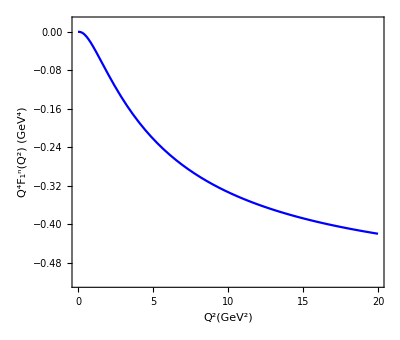

```mathematica
fig["neutron FF"]["1"]=Plot[Q2^2 F["neutron"]["1"][Q2],{Q2,0,20},PlotRange->{-0.52,0.02},Frame->True,FrameStyle->Thickness[0.003],LabelStyle->16,AspectRatio->0.85,PlotStyle->{Blue,Thickness[0.004]},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^4F_1^n(Q^2) (GeV^4)",18]}]
```

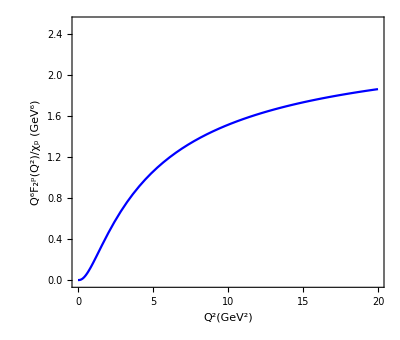

```mathematica
fig["proton FF"]["2"]=Plot[Q2^3 F["proton"]["2"][Q2]/Xp/.{Xp->1.793},{Q2,0,20},PlotRange->{-0.02,2.52},Frame->True,FrameStyle->Thickness[0.003],LabelStyle->16,AspectRatio->0.85,PlotStyle->{Blue,Thickness[0.004]},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^6F_2^p(Q^2)/χ_p (GeV^6)",18]}]
```

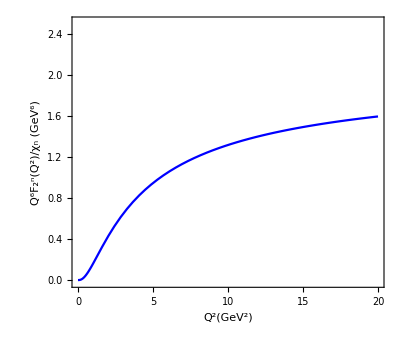

```mathematica
fig["neutron FF"]["2"]=Plot[Q2^3 F["neutron"]["2"][Q2]/Xn/.{Xn->-1.913},{Q2,0,20},PlotRange->{-0.02,2.52},Frame->True,FrameStyle->Thickness[0.003],LabelStyle->16,AspectRatio->0.85,PlotStyle->{Blue,Thickness[0.004]},FrameLabel->{Style["Q^2(GeV^2)",18],Style["Q^6F_2^n(Q^2)/χ_n (GeV^6)",18]}]
```

```mathematica
Clear[grid];
grid={};
For[i=0,i<100,i=i+1,
XX=0.005+0.01 i;
a0=0.507;
YY={XX H["proton"]["u"][XX,1],XX H["proton"]["u"][XX,4],XX H["proton"]["u"][XX,10]};
a0=0.541;
YY1={XX H["proton"]["u"][XX,1],XX H["proton"]["u"][XX,4],XX H["proton"]["u"][XX,10]};
a0=0.473;
YY2={XX H["proton"]["u"][XX,1],XX H["proton"]["u"][XX,4],XX H["proton"]["u"][XX,10]};
grid=Join[grid,{{XX,YY[[1]],YY1[[1]],YY2[[1]],YY[[2]],YY1[[2]],YY2[[2]],YY[[3]],YY1[[3]],YY2[[3]]}}]];
Export[dir<>"grid_proton_gpd_hu.dat",grid,"Table"];
Clear[grid,XX,YY,YY1,YY2,i];
```

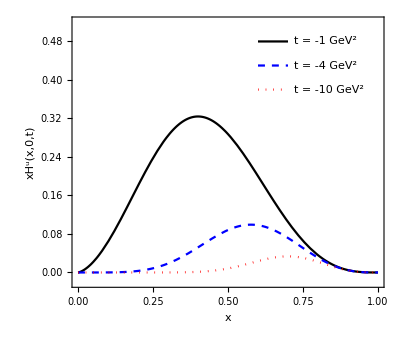

```mathematica
a0=0.507;
fig["proton GPD"]["Hu"]=Show[Plot[{x H["proton"]["u"][x,1],x H["proton"]["u"][x,4], x H["proton"]["u"][x,10]},{x,0,1},Frame->True,FrameStyle->Thickness[0.003],PlotStyle->{{Black,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Dotted,Thickness[0.004]}},LabelStyle->16,AspectRatio->0.85,PlotRange->{Full,{-0.02,0.52}},FrameLabel->{Style["x",18],Style["xH^u(x,0,t)",18]},Axes->True,LabelStyle->12],
Graphics[{{Black,Thickness[0.004],Line[{{0.6,0.48},{0.7,0.48}}]},{FontSize->14,Text["t = -1 GeV^2",{0.72,0.48},Left]}}],
Graphics[{{Blue,Thickness[0.004],Dashed,Line[{{0.6,0.43},{0.7,0.43}}]},{FontSize->14,Text["t = -4 GeV^2",{0.72,0.43},Left]}}],
Graphics[{{Red,Thickness[0.004],Dotted,Line[{{0.6,0.38},{0.7,0.38}}]},{FontSize->14,Text["t = -10 GeV^2",{0.72,0.38},Left]}}]]
```

```mathematica
Clear[grid];
grid={};
For[i=0,i<100,i=i+1,
XX=0.005+0.01 i;
a0=0.507;
YY={XX H["proton"]["d"][XX,1],XX H["proton"]["d"][XX,4],XX H["proton"]["d"][XX,10]};
a0=0.541;
YY1={XX H["proton"]["d"][XX,1],XX H["proton"]["d"][XX,4],XX H["proton"]["d"][XX,10]};
a0=0.473;
YY2={XX H["proton"]["d"][XX,1],XX H["proton"]["d"][XX,4],XX H["proton"]["d"][XX,10]};
grid=Join[grid,{{XX,YY[[1]],YY1[[1]],YY2[[1]],YY[[2]],YY1[[2]],YY2[[2]],YY[[3]],YY1[[3]],YY2[[3]]}}]];
Export[dir<>"grid_proton_gpd_hd.dat",grid,"Table"];
Clear[grid,XX,YY,YY1,YY2,i];
```

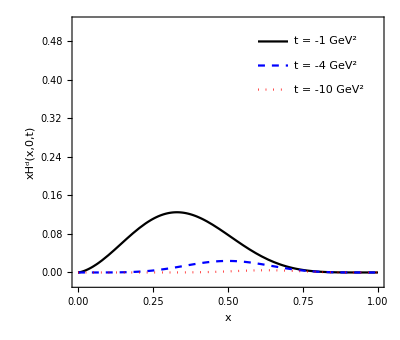

```mathematica
a0=0.507;
fig["proton GPD"]["Hd"]=Show[Plot[{x H["proton"]["d"][x,1],x H["proton"]["d"][x,4],x H["proton"]["d"][x,10]},{x,0,1},Frame->True,FrameStyle->Thickness[0.003],PlotStyle->{{Black,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Dotted,Thickness[0.004]}},LabelStyle->16,AspectRatio->0.85,PlotRange->{Full,{-0.02,0.52}},FrameLabel->{Style["x",18],Style["xH^d(x,0,t)",18]},Axes->True,LabelStyle->12],
Graphics[{{Black,Thickness[0.004],Line[{{0.6,0.48},{0.7,0.48}}]},{FontSize->14,Text["t = -1 GeV^2",{0.72,0.48},Left]}}],
Graphics[{{Blue,Thickness[0.004],Dashed,Line[{{0.6,0.43},{0.7,0.43}}]},{FontSize->14,Text["t = -4 GeV^2",{0.72,0.43},Left]}}],
Graphics[{{Red,Thickness[0.004],Dotted,Line[{{0.6,0.38},{0.7,0.38}}]},{FontSize->14,Text["t = -10 GeV^2",{0.72,0.38},Left]}}]]
```

```mathematica
Clear[grid];
grid={};
For[i=0,i<100,i=i+1,
XX=0.005+0.01 i;
a0=0.507;
YY={XX EE["proton"]["u"][XX,1],XX EE["proton"]["u"][XX,4],XX EE["proton"]["u"][XX,10]}/1.673;
a0=0.541;
YY1={XX EE["proton"]["u"][XX,1],XX EE["proton"]["u"][XX,4],XX EE["proton"]["u"][XX,10]}/1.673;
a0=0.473;
YY2={XX EE["proton"]["u"][XX,1],XX EE["proton"]["u"][XX,4],XX EE["proton"]["u"][XX,10]}/1.673;
grid=Join[grid,{{XX,YY[[1]],YY1[[1]],YY2[[1]],YY[[2]],YY1[[2]],YY2[[2]],YY[[3]],YY1[[3]],YY2[[3]]}}]];
Export[dir<>"grid_proton_gpd_eu.dat",grid,"Table"];
Clear[grid,XX,YY,YY1,YY2,i];
```

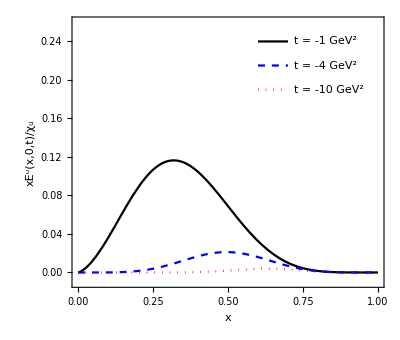

```mathematica
a0=0.507;
fig["proton GPD"]["Eu"]=Show[Plot[{x (EE["proton"]["u"][x,1])/(Xu/.{Xu->1.673}),x (EE["proton"]["u"][x,4])/(Xu/.{Xu->1.673}), x (EE["proton"]["u"][x,10])/(Xu/.{Xu->1.673})},{x,0,1},Frame->True,FrameStyle->Thickness[0.003],PlotStyle->{{Black,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Dotted,Thickness[0.004]}},LabelStyle->16,AspectRatio->0.85,PlotRange->{Full,{-0.01,0.26}},FrameLabel->{Style["x",18],Style["xE^u(x,0,t)/χ_u",18]},Axes->True,LabelStyle->12],
Graphics[{{Black,Thickness[0.004],Line[{{0.6,0.48/2},{0.7,0.48/2}}]},{FontSize->14,Text["t = -1 GeV^2",{0.72,0.48/2},Left]}}],
Graphics[{{Blue,Thickness[0.004],Dashed,Line[{{0.6,0.43/2},{0.7,0.43/2}}]},{FontSize->14,Text["t = -4 GeV^2",{0.72,0.43/2},Left]}}],
Graphics[{{Red,Thickness[0.004],Dotted,Line[{{0.6,0.38/2},{0.7,0.38/2}}]},{FontSize->14,Text["t = -10 GeV^2",{0.72,0.38/2},Left]}}]]
```

```mathematica
Clear[grid];
grid={};
For[i=0,i<100,i=i+1,
XX=0.005+0.01 i;
a0=0.507;
YY={XX EE["proton"]["d"][XX,1],XX EE["proton"]["d"][XX,4],XX EE["proton"]["d"][XX,10]}/-2.033;
a0=0.541;
YY1={XX EE["proton"]["d"][XX,1],XX EE["proton"]["d"][XX,4],XX EE["proton"]["d"][XX,10]}/-2.033;
a0=0.473;
YY2={XX EE["proton"]["d"][XX,1],XX EE["proton"]["d"][XX,4],XX EE["proton"]["d"][XX,10]}/-2.033;
grid=Join[grid,{{XX,YY[[1]],YY1[[1]],YY2[[1]],YY[[2]],YY1[[2]],YY2[[2]],YY[[3]],YY1[[3]],YY2[[3]]}}]];
Export[dir<>"grid_proton_gpd_ed.dat",grid,"Table"];
Clear[grid,XX,YY,YY1,YY2,i];
```

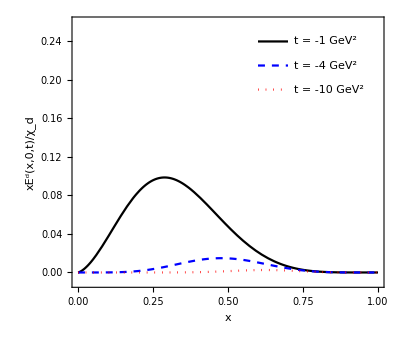

```mathematica
a0=0.507;
fig["proton GPD"]["Ed"]=Show[Plot[{x (EE["proton"]["d"][x,1])/(Xd/.{Xd->-2.033}),x (EE["proton"]["d"][x,4])/(Xd/.{Xd->-2.033}), x (EE["proton"]["d"][x,10])/(Xd/.{Xd->-2.033})},{x,0,1},Frame->True,FrameStyle->Thickness[0.003],PlotStyle->{{Black,Thickness[0.004]},{Blue,Dashed,Thickness[0.004]},{Red,Dotted,Thickness[0.004]}},LabelStyle->16,AspectRatio->0.85,PlotRange->{Full,{-0.01,0.26}},FrameLabel->{Style["x",18],Style["xE^d(x,0,t)/χ_d",18]},Axes->True,LabelStyle->12],
Graphics[{{Black,Thickness[0.004],Line[{{0.6,0.48/2},{0.7,0.48/2}}]},{FontSize->14,Text["t = -1 GeV^2",{0.72,0.48/2},Left]}}],
Graphics[{{Blue,Thickness[0.004],Dashed,Line[{{0.6,0.43/2},{0.7,0.43/2}}]},{FontSize->14,Text["t = -4 GeV^2",{0.72,0.43/2},Left]}}],
Graphics[{{Red,Thickness[0.004],Dotted,Line[{{0.6,0.38/2},{0.7,0.38/2}}]},{FontSize->14,Text["t = -10 GeV^2",{0.72,0.38/2},Left]}}]]
```

```mathematica
a0=0.507;
CoolColor[z_]:=RGBColor[z,1-z,1];
fig["proton GPD/PDF"]["Hu"]=Plot3D[H["proton"]["u"][x,Q2]/H["proton"]["u"][x,0],{x,0,1},{Q2,10,0},LabelStyle->16,BoxRatios->{1,1,0.5},PlotRange->{Full,Full,{-0.02,1.02}},Axes->True,LabelStyle->12,AxesLabel->{Style["x",18],Style["-t (GeV^2)",18]},PlotLabel->Style["H^u(x,0,t)/f^u(x)",18],ColorFunction->CoolColor]
```

-Graphics3D-

```mathematica
a0=0.507;
CoolColor[z_]:=RGBColor[z,1-z,1];
fig["proton GPD/PDF"]["Hd"]=Plot3D[H["proton"]["d"][x,Q2]/H["proton"]["d"][x,0],{x,0,1},{Q2,10,0},LabelStyle->16,BoxRatios->{1,1,0.5},PlotRange->{Full,Full,{-0.02,1.02}},Axes->True,LabelStyle->12,AxesLabel->{Style["x",18],Style["-t (GeV^2)",18]},PlotLabel->Style["H^d(x,0,t)/f^d(x)",18],ColorFunction->CoolColor]
```

-Graphics3D-

```mathematica
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_f1.png",fig["proton FF"]["1"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/neutron_f1.png",fig["neutron FF"]["1"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_f2.png",fig["proton FF"]["2"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/neutron_f2.png",fig["neutron FF"]["2"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_hu.png",fig["proton GPD"]["Hu"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_hd.png",fig["proton GPD"]["Hd"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_eu.png",fig["proton GPD"]["Eu"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_ed.png",fig["proton GPD"]["Ed"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_hfratiou.png",fig["proton GPD/PDF"]["Hu"]];
Export["/Users/user/Liu/Repos/LFHQCD/notebook/proton_hfratiod.png",fig["proton GPD/PDF"]["Hd"]];
```

```mathematica
InverseFourierTransform[Exp[-(b1^2+b2^2) A],{b1,b2},{k1,k2},FourierParameters->{-1,1},Assumptions->{A>0}]
```

(ⅇ^(-(k1^2+k2^2)/(4 A)) π)/A

## Test

```mathematica
β0=11-2/3 nf;
β1=102-38/3 nf;
```

```mathematica
α[μ_]:=((4 π)/(β0 Log[t]) (1-β1/β0^2 Log[Log[t]]/Log[t]))/.{t->μ^2/Λ^2};
```

```mathematica
NSolve[(α[t]/.{nf->5})==118/1000,t,Reals]
```

{{t→162464.}}

```mathematica
NSolve[(12 π (1-(348 Log[Log[t]])/(529 Log[t])))/(23 Log[t])==0.118,t,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{t→162464.}}

```mathematica
α[4.2]/.{nf->5,Λ->0.226}
```

0.224715

```mathematica
NSolve[(α[4.2]/.{nf->4,Λ->Λ0})==(α[4.2]/.{nf->5,Λ->0.226}),Λ0,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Λ0→-0.323153},{Λ0→0.323153}}

```mathematica
α[4.2]/.{nf->4,Λ->0.323}
```

0.224679

```mathematica
NSolve[(α[1.3]/.{nf->3,Λ->Λ0})==(α[1.3]/.{nf->4,Λ->0.323}),Λ0,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Λ0→-0.36962},{Λ0→0.36962}}

```mathematica
NSolve[Log[1/x]==0.0001,x]
```

{{x→0.9999}}

```mathematica
Log[10^3*1.0]
```

6.90776

```mathematica
Integrate[x^a (1-x)^b Log[1/x],{x,0,1},Assumptions->{a>-1,b>0}]//TraditionalForm
```

-(a+1 b+1 (a-a+b+1))/(a+b+2)

```mathematica
Integrate[(x^a (1-x)^b Log[1/x]/(Beta[a+1,b+1] (PolyGamma[a+b+2]-PolyGamma[a+1])))/.{a->1/2,b->2.},{x,0,1}]
```

1.

```mathematica
N[(Beta[a+1,b+1] (PolyGamma[a+b+2]-PolyGamma[a+1]))/.{a->0.5,b->2.67}]
```

0.172906

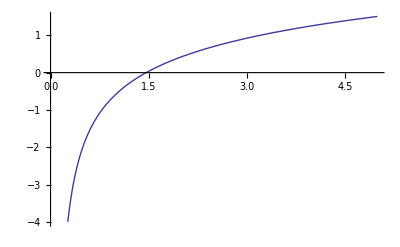

```mathematica
Plot[PolyGamma[x],{x,0,5}]
```

```mathematica
N[EulerGamma,3]
```

0.577

```mathematica
NIntegrate[(x^a (1-x)^b Log[1/x]/(Beta[a+1,b+1] (PolyGamma[a+b+1]-PolyGamma[a+1])))/.{a->0.5,b->2.67},{x,10^-4,1}]
```

1.18926

```mathematica
HarmonicNumber[1.7]-EulerGamma-PolyGamma[2.7]
```

-1.11022×10^-16

```mathematica
Integrate[Log[x],{x,0,1}]
```

-1

```mathematica
Integrate[Exp[-kt^2/(2 λ) Log[1/x]/(1-x)^2] kt,{kt,0,Infinity},Assumptions->{λ>0,x>0,x<1}]
```

-((-1+x)^2 λ)/Log[x]

```mathematica
NIntegrate[(Gamma[τ-1/2]/(√π Gamma[τ-1]) x^(-1/2)(1-x)^(τ-2) Exp[-1/λ (m1^2/x+m2^2/(1-x)) (x Log[1/x])/(1-x)])/.{τ->6,λ->0.5682^2,m1->0.2,m2->0.4},{x,0,1}]
```

0.561944

```mathematica
Integrate[Exp[-1/λ (m1^2/x+m2^2/(1-x)) (x Log[1/x])/(1-x)],{x,0,1},Assumptions->{λ>0,m1>0,m2>0}]
```

Integrate[(1/x)^(-((m2^2/(1-x)+m1^2/x) x)/((1-x) λ)),{x,0,1},Assumptions→{λ>0,m1>0,m2>0}]

```mathematica
Integrate[Gamma[τ-1/2]/(√π Gamma[τ-1]) x^(-1/2)(1-x)^(τ-2) ,{x,0,1},Assumptions->{τ>1}]
```

1

```mathematica
Sqrt[10.]
```

3.16228

```mathematica
ϕ[x_,σ_,μ_]:=1/(√(2 π))Exp[-1/(2 σ^2)(x-μ)^2];
```

```mathematica
Integrate[ϕ[x,1,0],{x,-k,k}]/.{k->1.7}
```

0.910869

```mathematica
Integrate[x^(α-1) (1-x)^β+γ (2 x^2)/(9 M^2),{x,0,1},Assumptions->{α>0,β>0}]
```

(2 γ)/(27 M^2)+(Gamma[α] Gamma[1+β])/Gamma[1+α+β]

```mathematica
v[x_,α_,β_,γ_]:=(x^α (1-x)^β+γ (2 x^2)/(9 M^2))/((2 γ)/(27 M^2)+Beta[α,1+β])
```

```mathematica
(D[v[x,α,β,γ],α]//FullSimplify)//TraditionalForm
```

(27 M^2 (x^α (1-x)^β (27 M^2 αβ+1 (0α+β+1-0α+log(x))+2 γ log(x))+6 γ x^2 (0α+β+1-0α) αβ+1))/((2 γ+27 M^2 αβ+1)^2)

```mathematica
Integrate[(v[x,α,β,γ])/.{α->0.70,β->1.54,γ->0.60,M->5.2},{x,0,1}]
```

0.217877

```mathematica
fs=OpenWrite["/Users/user/Desktop/hoppet-1.1.5/mycode/results/pion_parameterization_Q=5.2.dat"];
WriteString[fs,"PRC72(2005)065203 prefered parameterization Q=5.2GeV\n"];
WriteString[fs,"x\txv\tdxv\n"];
sep="  ";
For[i=0,i<1000,i++,
x0=0.0005+0.001 i;
xv=v[x0,0.70,1.54,0.60]/.{M->5.2};
dxv2=((D[v[x,α,β,γ],α])^2 0.06^2+(D[v[x,α,β,γ],β])^2 0.08^2+(D[v[x,α,β,γ],γ])^2 0.34^2)/.{x->x0,α->0.70,β->1.54,γ->0.60,M->5.2};
WriteString[fs,x0,"\t",N[xv,6],"\t",N[Sqrt[dxv2],6],"\n"]
];
Close[fs];
```

```mathematica
α
```

α

```mathematica
Clear[fs]
```

```mathematica
afd
```

```mathematica
FX[x_]:=x^(-1/2) ((1-γ)/2+15/16 γ (1-x)^2) (x (1-x))^η;
```

```mathematica
Integrate[FX[x],{x,0,1},Assumptions->{η>0}]
```

(4^(-2-η) √π (30+η (32 (2+η)-γ (19+17 η))) Gamma[1+2 η])/Gamma[7/2+2 η]

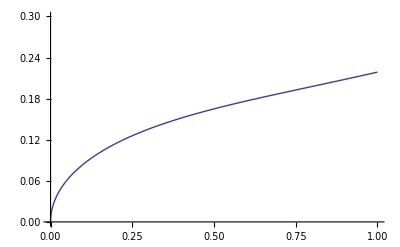

```mathematica
Plot[(x^(1/2)/2 ((1-γ)/2+15/16 γ (1-x)^2))/.{γ->0.125},{x,0,1},PlotRange->{0,0.3}]
```

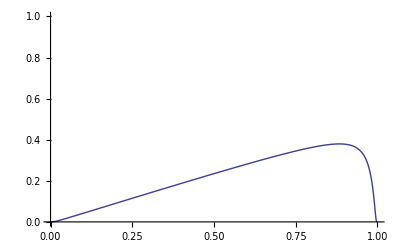

```mathematica
Plot[(x/2 Exp[-m^2/(x (1-x))])/.{m->0.125},{x,0,1},PlotRange->{0,1}]
```

```mathematica
Integrate[1/1.193(x^(α-1) (1-x)^β (1+γ x^2))/.{α->0.7,β->2.03,γ->13.8},{x,0,1}]
```

1.00011